## System

### A 2D hexagonal lattice, of size [nmax × nmax × 2], with onsite Anderson disorder of strength u. Periodic boundary conditions.

```mathematica
Clear[H0,δH,H];  
nmax=100;
H0=With[{k={1,-1}0},(#+#†)&@ArrayFlatten@ArrayFlatten@SparseArray[
Flatten@Table[{If[i==nmax,{1,i, j,j,1,2}->1. ⅇ^(ⅈ k[[1]]),{i+1,i, j,j,1,2}->1.],If[j==nmax,{i,i, 1,j,1,2}->1. ⅇ^(ⅈ k[[2]]),{i,i,j+1,j,1,2}->1.],{i,i,j,j,1,2}->1.},{i,1,nmax},{j,1,nmax}],{nmax,nmax,nmax,nmax,2,2}]];
δH=SparseArray[{i_,i_}:>RandomReal[{-1,1}],{2 nmax^2,2 nmax^2}]
H[u_]:=H0(*+u δH*)
vx=(#+#†)&@ArrayFlatten@ArrayFlatten@SparseArray[
Flatten@Table[{If[i==nmax,{1,i, j,j,1,2}->ⅈ(√3.)/2,{i+1,i, j,j,1,2}->ⅈ(√3.)/2],If[j==nmax,{i,i, 1,j,1,2}->-ⅈ(√3.)/2,{i,i,j+1,j,1,2}->-ⅈ(√3.)/2],{i,i,j,j,1,2}->0.},{i,1,nmax},{j,1,nmax}],{nmax,nmax,nmax,nmax,2,2}];
```

SparseArray[<20000>,{20000,20000}]

#### Analytic DOS

From Yuan et al, Phys. Rev. B 82, 115448 (2010)

```mathematica
AnalyticDOS[ϵt_]:=Module[{F=(1+Abs@ϵt)^2-((ϵt^2-1)^2)/4},
Piecewise[{{(2Abs@ϵt)/π^2 1/(√F)EllipticK[(4 Abs@ϵt)/F],Abs@ϵt≤1},{(2Abs@ϵt)/π^2 1/(√(4Abs@ϵt))EllipticK[F/(4 Abs@ϵt)], 1<Abs@ϵt≤3}},0]]
```

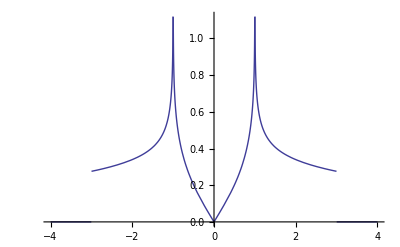

```mathematica
Plot[AnalyticDOS[ϵt],{ϵt,-4,4}]
```

#### What is the optimal sampling for a Chebyshev expansion of order N? Answer: ϵ_m=Cos[ϕ_m], with ϕ_m=π(m-1/2)/(N+1), m=1...N+1 (i.e. the zeroes of T_(N+1))

Without an upper cutoff for the Chebyshev expansion, we resolve a proper Dirac delta function
	δ(ϵ-ϵ’)=∑_n^∞ 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 
If we truncate the sum, can we expect to still have a delta function if we constrain ϵ to a certain mesh? Yes, like in a Fourier transform→Fourier series.
To find the mesh, we use T_n(Cos[ϕ])=Cos[n ϕ], and the zeroes of T_(N+1)(ϵ) are ϵ_m=Cos[ϕ_m], with ϕ_m=π(m+1/2)/(N+1), m=1 ... N+1.
Then, using the identity
	2/(N+1) ∑_(n=0)^N 1/ν_n Cos[n ϕ_m]Cos[n ϕ_m']=δ_mm' for m=1.. N+1.
we can write
	2/(N+1) ∑_(n=0)^N 1/ν_n T_n[ϵ_sm]T_n[ϵ_s'm']=δ_(ϵ_m-ϵ_m')
The above is a Kronecker delta, instead of a Dirac Delta. Note the absence of N(ϵ) in the expression above. To get a Dirac delta again, we weight by the inverse of
dϵ_m=|ϵ_(m+1)-ϵ_m| =2Sin[π/(2(N+1))] Sin[(m π)/(N+1)] ≈ π/(N+1)√(1-ϵ_m^2)+O(N^-2). This gives, for large N, what we knew.
	1/dϵ_m2/(N+1) ∑_(n=0)^N 1/ν_n T_n[ϵ_sm]T_n[ϵ_s'm']≈∑_(n=0)^N 1/ν_n N(ϵ_m)T_n[ϵ_sm]T_n[ϵ_s'm']≈δ(ϵ_m-ϵ_m')
The code below demonstrates the δ_(ϵ_m-ϵ_m') relation

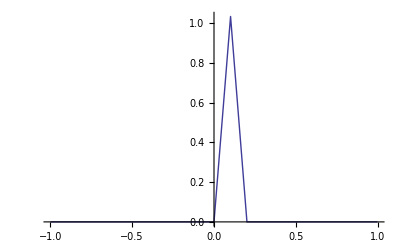

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;2/NN ch1.ch2 ]
Sort@With[{NN=30,m=15},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@Range[1,NN+1]];
ListLinePlot[%, PlotRange->All]
```

```mathematica
ϵmesh[4]
ChebyshevT[5,ϵmesh[4]]
```

{-0.951057,-0.587785,6.12323×10^-17,0.587785,0.951057}

{6.66134×10^-16,-6.66134×10^-16,3.06162×10^-16,1.11022×10^-16,-6.66134×10^-16}

There is an important problem with this sampling however: it only gives a clean resolution of δ(ϵ-ϵ’) when both ϵ and ϵ’ are points in the mesh. In the case of δ(ϵ_m-h), the eigenvalues of h are not in the mesh, and the resolution is no cleaner than a random mesh in this case (except at those points in which eigenvalues of h fall in the mesh, of course). See code below.

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
(*ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];*)
ϵmesh0[NN_]:=Sort@Range[-1,1,1/Round[NN/π]]
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]
δKCh[ϵ_,ϵp_,NN_Integer]:=Module[{ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;2/NN ch1.ch2 ]
Manipulate[ListLinePlot[#,PlotRange->All]&@Sort@With[{NN=30},{{ϵmesh[NN],δKCh[#,ϵp,NN]&/@ϵmesh[NN]}ᵀ,{ϵmesh0[NN],δKCh[#,ϵp,NN]&/@ϵmesh0[NN]}ᵀ}],{{ϵp,0},-1,1}]
```

Nevertheless, using this sampling gives a clean F(ϵ_m,ϵ_m'), while any other sampling has artifacts. This is the F(ϵ_m,ϵ_m') with a proper mesh

-Graphics-

... while this is the same with a uniform mesh

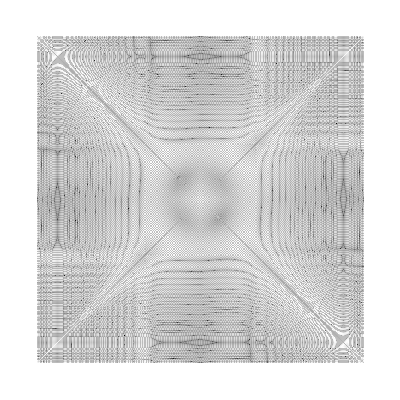

-Graphics-

The extra beating oscillating sign can be filtered out by a simple convolution

```mathematica
KuboσF[Mean[tempK600], InterpolationOrder->0];
Manipulate[ListLinePlot[{Diagonal[#,200],Diagonal[#,201]}, PlotRange->{-1,1}z]&@ListCorrelate[1/(γ+4(α+β))({{β/4, α/4, β/4}, {α/4, γ, α/4}, {β/4, α/4, β/4}}),temp],{{α,1},0,3},{{β,0},-3,3},{{γ,1},0,3},{z,0,.01}]
(*ArrayPlot[Log@%%]*)
```

#### Tests

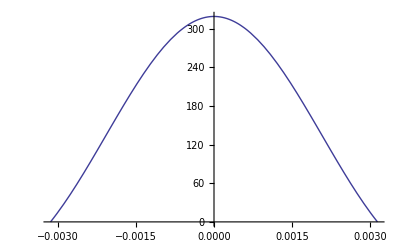

```mathematica
Clear@ChebyVec;
ChebyVec=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
Clear@δCh;
δCh[ϵ_?NumericQ,n_Integer]:=ChebyVec[ϵ,n].ChebyVec[0,n] π/2
δW[n_Integer]:=√NIntegrate[δCh[ϵ,n] ϵ^2,{ϵ,-.999,.999}, MaxRecursion->60]
With[{n=1000},Plot[δCh[ϵ,n],{ϵ,-π/n,π/n}, PlotRange->All]]
```

```mathematica
Cos[π(Range[3])/3]
```

{1/2,-1/2,-1}

```mathematica
With[{n=10},ChebyVec[#,n]&/@Cos[π(Range[n]-1/2)/n]]
With[{n=10.},Cos[π(Range[n])/n]]
```

{{4.06956,4.01946,3.87038,3.62601,3.29234,2.87761,2.39203,1.84754,1.25756,0.63662,9.03624×10^-15},{1.40228,1.24944,0.824237,0.219364,-0.433327,-0.991559,-1.33364,-1.38501,-1.13446,-0.63662,-1.08979×10^-15},{0.900316,0.63662,-1.9991×10^-16,-0.63662,-0.900316,-0.63662,5.99731×10^-16,0.63662,0.900316,0.63662,-8.99597×10^-16},{0.714495,0.324374,-0.41997,-0.705698,-0.220791,0.505224,0.679525,0.111772,-0.578039,-0.63662,3.173×10^-16},{0.644555,0.100831,-0.613009,-0.292622,0.521456,0.455769,-0.37886,-0.574303,0.199179,0.63662,-3.578×10^-17},{0.644555,-0.100831,-0.613009,0.292622,0.521456,-0.455769,-0.37886,0.574303,0.199179,-0.63662,-3.578×10^-17},{0.714495,-0.324374,-0.41997,0.705698,-0.220791,-0.505224,0.679525,-0.111772,-0.578039,0.63662,3.173×10^-16},{0.900316,-0.63662,-1.9991×10^-16,0.63662,-0.900316,0.63662,5.99731×10^-16,-0.63662,0.900316,-0.63662,-8.99597×10^-16},{1.40228,-1.24944,0.824237,-0.219364,-0.433327,0.991559,-1.33364,1.38501,-1.13446,0.63662,-1.08979×10^-15},{4.06956,-4.01946,3.87038,-3.62601,3.29234,-2.87761,2.39203,-1.84754,1.25756,-0.63662,9.03624×10^-15}}

{0.951057,0.809017,0.587785,0.309017,6.12323×10^-17,-0.309017,-0.587785,-0.809017,-0.951057,-1.}

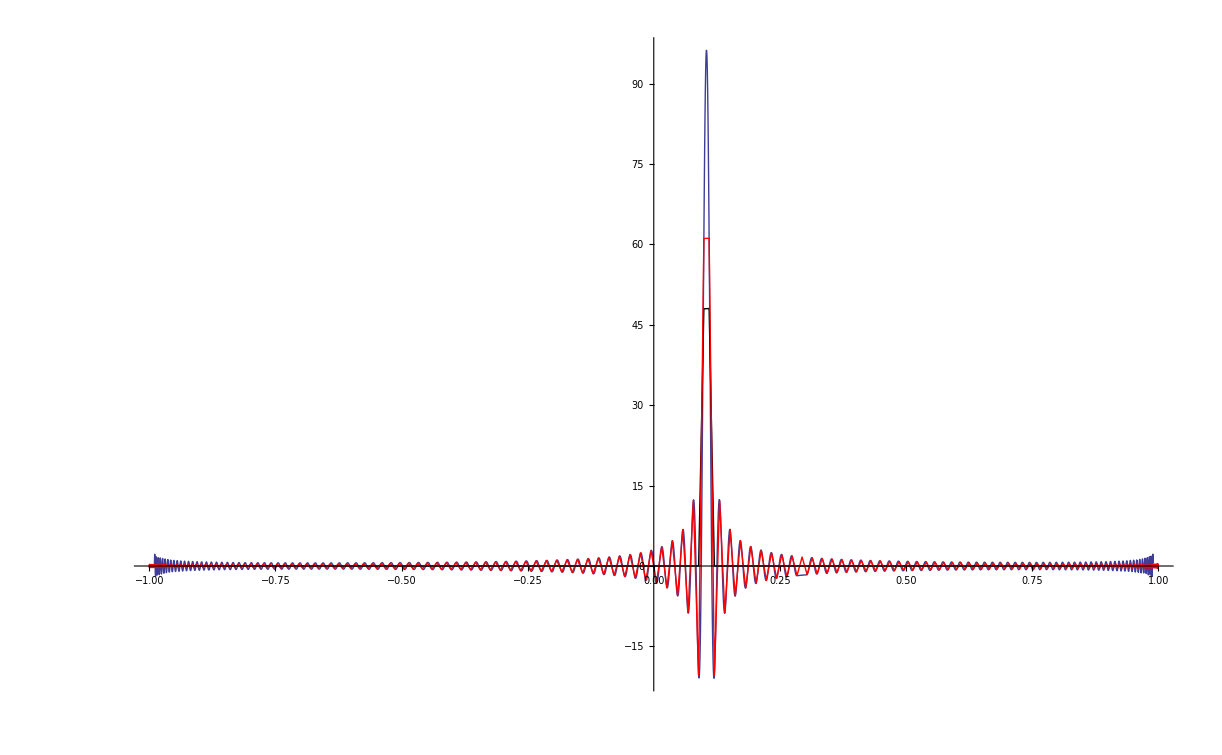

```mathematica
Clear@δCh2;
δCh2[ϵ_?NumericQ,n_Integer,m_Integer]:=Module[{ch1=ChebyVec[ϵ,n],ϵp=Cos[π(m/2-.5)/n],ch2},ch2=ChebyVec[ϵp,n]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))^-1]
With[{n=300, m=281},Plot[δCh2[ϵ,n,m],{ϵ,-.99,.99}, PlotRange->All, Epilog->{Line[{#,(δCh2[#,n,m-1]+δCh2[#,n,m+1])/2}&/@Cos[π(Range[n]-.5)/n]],Red,Line[{#,δCh2[#,n,m]}&/@Cos[π(Range[n]-.5)/n]]}]]
```

```mathematica
NIntegrate[δCh2[ϵ,300,280],{ϵ,-1,1}]
```

1.

0.999982

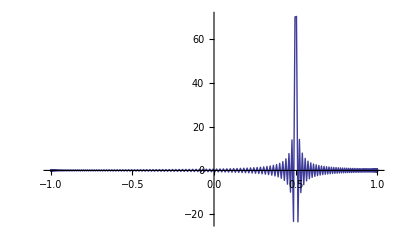

```mathematica
With[{n=300,m=201},{#,δCh2[#,n,m]}&/@Cos[π(Range[n]-.5)/n]];
Total@Table[(%[[n,1]]-%[[n+1,1]])(%[[n+1,2]]+%[[n,2]])/2,{n,1,Length[%]-1}]
ListLinePlot[%%,PlotRange->All]
```

0.999982

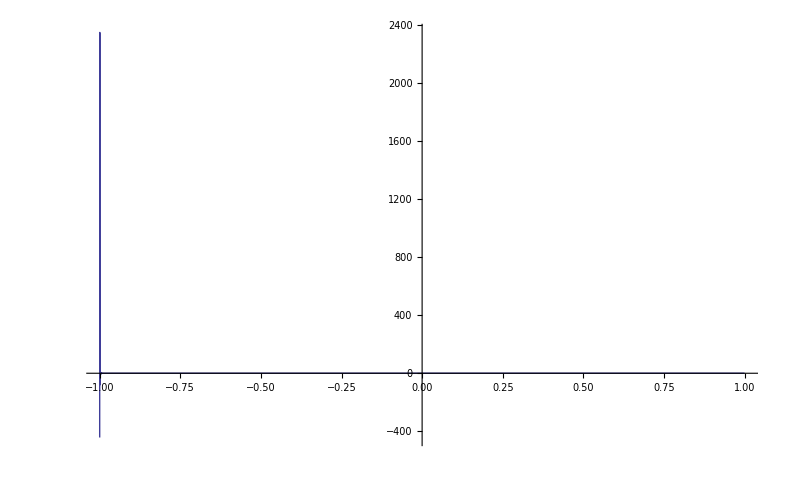

```mathematica
δCh2[ϵ_?NumericQ,n_Integer,m_Integer]:=Module[{ch1=ChebyVec[ϵ,n],ϵp=Sign[m]Cos[π(m/2-.5)/n],ch2},ch2=ChebyVec[ϵp,n]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))^-1]
With[{n=300,m=-4},{#,(δCh2[#,n,m-1]+δCh2[#,n,m+1])/2}&/@Cos[π(Range[1,n]-.5)/n]];
Total@Table[(%[[n,1]]-%[[n+1,1]])(%[[n+1,2]]+%[[n,2]])/2,{n,1,Length[%]-1}]
ListLinePlot[%%,PlotRange->All]
```

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::pspec: Part specification 1 + n is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

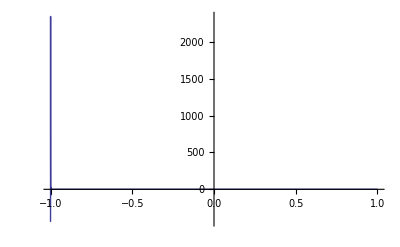
(-Graphics-)⟦n,1⟧-(-Graphics-)⟦1+n,1⟧

```mathematica
(%[[n,1]]-%[[n+1,1]])
```

```mathematica
FullSimplify[Cos[π(m-1/2)/n]-Cos[π(m+1-1/2)/n]]
```

2 Sin[π/(2 n)] Sin[(m π)/n]

{1.00632,0.983632,0.983632}

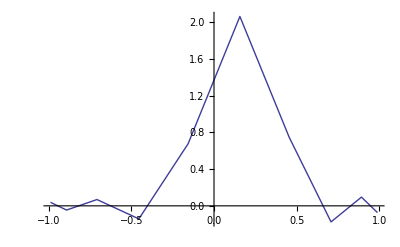

```mathematica
δCh2[ϵ_?NumericQ,n_Integer,m_Integer]:=Module[{ch1=ChebyVec[ϵ,n],ϵp=Sign[m]Cos[π(m/2-.5)/n],ch2},ch2=ChebyVec[ϵp,n]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))^-1]
With[{n=10,m=-90},{#,(δCh2[#,n,m-1]+δCh2[#,n,m+1])/2}&/@Cos[π(Range[1,n]-.5)/n]];
With[{NN=10},{
Total@Table[2 Sin[π/(2 NN)] Sin[(m π)/NN]%[[m,2]],{m,1,NN}],
Total@Table[2 Sin[π/(2 NN)] Sin[(m π)/NN](%[[m+1,2]]+%[[m,2]])/2,{m,1,NN-1}],
Total@Table[2 Sin[π/(2 NN)] Sin[(m π)/NN](%[[m+1,2]]+%[[m,2]])/2,{m,1,NN-1}]}]
ListLinePlot[%%,PlotRange->All]
```

```mathematica
Sign[1]Cos[π(1/2-.5)/100]
```

1.

2 Sin[π/(2 NN)] √(Sin[(π Abs[m])/NN] Sin[(π Abs[mp])/NN])

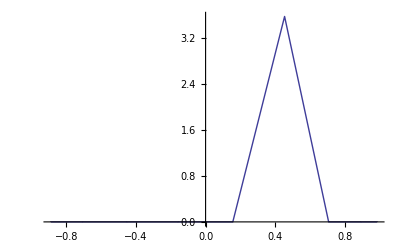

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-.5)/NN];
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵ2=ϵmesh[m+1,NN],ϵp=ϵmesh[mp,NN],ϵp2=ϵmesh[mp+1,NN],ch1,ch2},ch1=(ChebyVecBare[ϵ,NN]+ChebyVecBare[ϵ2,NN])/2;ch2=(ChebyVecBare[ϵp,NN]+ChebyVecBare[ϵp2,NN])/2; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))]
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;ch1.ch2 √((2/(π √(1-ϵp^2)))(2/(π √(1-ϵ^2))))]
Δ[m_Integer,mp_Integer,NN_Integer]=2Sin[π/(2NN)] √(Sin[(Abs[m] π)/NN]Sin[(Abs[mp] π)/NN])
With[{NN=10,m=-6},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@Join[Range[-NN+1,-1],Range[1,NN-1]]];
ListLinePlot[Sort@%, PlotRange->All]
```

```mathematica
ChebyshevT[6,-Cos[2.]]/Cos[6 2.]
```

1.

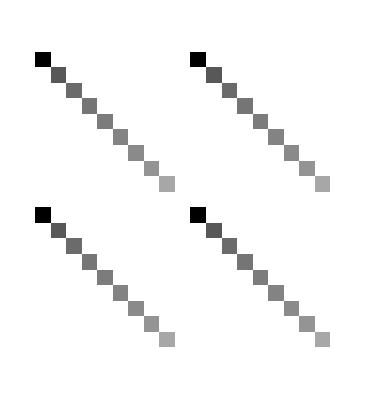

```mathematica
With[{NN=10},Table[Δ[m,mp,NN]δKCh[m,mp,NN],{m,-NN,NN},{mp,-NN+1,NN}]]//ArrayPlot
```

```mathematica
.
```

```mathematica
With[{NN=100,m=81},{ϵmesh[#,NN],DD[m,#,NN]}&/@Range[-NN,NN]];
ListLinePlot[%,PlotRange->All]
```

-Graphics-

```mathematica
With[{NN=300},ChebyshevT[NN,#]&/@Cos[π(Range[1,NN]-.5)/NN]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

We will use a discrete, non-uniform ϵ mesh for F(ϵ,ϵ’). We will take ϵ_m=Sign[m]Cos[π(m-1/2)/N], with |m|=1...N, i.e. the zeroes of the N-th Cheby polynomial, T_N(ϵ_m)=0. In this way, the continuous projector identity
	δ(ϵ-ϵ’)=∑_n 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 
turns into
	D_(m,m')= ∑_n 1/ν_n N(ϵ_m) T_n(ϵ_m)T_n(ϵ_m')=δ(ϵ_m-ϵ_m').
This is still a Dirac delta function, in the sense that ∫ dϵ δ(ϵ-ϵ_m')=1. However, using the above mesh, we also have a discrete Kronecker delta
	∑_m 2 Sin[π/(2 n)] Sin[(m π)/n]D_(m+1,m)=1
We can, however, turn this int

#### Tests

```mathematica
Sort@With[{n=100},{#,δCh2[#,n]}&/@Most@Cos[π(Range[n]-.5)/n]];
With[{NN=100},Total@Table[2./(π √(1-Cos[π(n-.5)/NN]^2))δCh2[Cos[π(n-.5)/NN],NN],{n,0,NN-1}]]
```

13.5145 δCh2[-0.99889,100]+8.11403 δCh2[-0.996917,100]+5.80147 δCh2[-0.993961,100]+4.5182 δCh2[-0.990024,100]+3.7028 δCh2[-0.985109,100]+3.13935 δCh2[-0.979223,100]+2.72706 δCh2[-0.97237,100]+2.4126 δCh2[-0.964557,100]+2.16508 δCh2[-0.955793,100]+1.96538 δCh2[-0.946085,100]+1.80103 δCh2[-0.935444,100]+1.66357 δCh2[-0.92388,100]+1.54702 δCh2[-0.911403,100]+1.44706 δCh2[-0.898028,100]+1.3605 δCh2[-0.883766,100]+1.28491 δCh2[-0.868632,100]+1.21841 δCh2[-0.85264,100]+1.15955 δCh2[-0.835807,100]+1.10715 δCh2[-0.81815,100]+1.06029 δCh2[-0.799685,100]+1.0182 δCh2[-0.78043,100]+0.980247 δCh2[-0.760406,100]+0.945926 δCh2[-0.739631,100]+0.914798 δCh2[-0.718126,100]+0.886501 δCh2[-0.695913,100]+0.860726 δCh2[-0.673013,100]+0.83721 δCh2[-0.649448,100]+0.815729 δCh2[-0.625243,100]+0.796089 δCh2[-0.60042,100]+0.778121 δCh2[-0.575005,100]+0.761682 δCh2[-0.549023,100]+0.746645 δCh2[-0.522499,100]+0.7329 δCh2[-0.495459,100]+0.720349 δCh2[-0.46793,100]+0.708909 δCh2[-0.439939,100]+0.698505 δCh2[-0.411514,100]+0.689072 δCh2[-0.382683,100]+0.680554 δCh2[-0.353475,100]+0.672899 δCh2[-0.323917,100]+0.666064 δCh2[-0.29404,100]+0.660012 δCh2[-0.263873,100]+0.654709 δCh2[-0.233445,100]+0.650128 δCh2[-0.202787,100]+0.646243 δCh2[-0.171929,100]+0.643035 δCh2[-0.140901,100]+0.640488 δCh2[-0.109734,100]+0.638588 δCh2[-0.0784591,100]+0.637327 δCh2[-0.0471065,100]+0.636698 δCh2[-0.0157073,100]+0.636698 δCh2[0.0157073,100]+0.637327 δCh2[0.0471065,100]+0.638588 δCh2[0.0784591,100]+0.640488 δCh2[0.109734,100]+0.643035 δCh2[0.140901,100]+0.646243 δCh2[0.171929,100]+0.650128 δCh2[0.202787,100]+0.654709 δCh2[0.233445,100]+0.660012 δCh2[0.263873,100]+0.666064 δCh2[0.29404,100]+0.672899 δCh2[0.323917,100]+0.680554 δCh2[0.353475,100]+0.689072 δCh2[0.382683,100]+0.698505 δCh2[0.411514,100]+0.708909 δCh2[0.439939,100]+0.720349 δCh2[0.46793,100]+0.7329 δCh2[0.495459,100]+0.746645 δCh2[0.522499,100]+0.761682 δCh2[0.549023,100]+0.778121 δCh2[0.575005,100]+0.796089 δCh2[0.60042,100]+0.815729 δCh2[0.625243,100]+0.83721 δCh2[0.649448,100]+0.860726 δCh2[0.673013,100]+0.886501 δCh2[0.695913,100]+0.914798 δCh2[0.718126,100]+0.945926 δCh2[0.739631,100]+0.980247 δCh2[0.760406,100]+1.0182 δCh2[0.78043,100]+1.06029 δCh2[0.799685,100]+1.10715 δCh2[0.81815,100]+1.15955 δCh2[0.835807,100]+1.21841 δCh2[0.85264,100]+1.28491 δCh2[0.868632,100]+1.3605 δCh2[0.883766,100]+1.44706 δCh2[0.898028,100]+1.54702 δCh2[0.911403,100]+1.66357 δCh2[0.92388,100]+1.80103 δCh2[0.935444,100]+1.96538 δCh2[0.946085,100]+2.16508 δCh2[0.955793,100]+2.4126 δCh2[0.964557,100]+2.72706 δCh2[0.97237,100]+3.13935 δCh2[0.979223,100]+3.7028 δCh2[0.985109,100]+4.5182 δCh2[0.990024,100]+5.80147 δCh2[0.993961,100]+8.11403 δCh2[0.996917,100]+13.5145 δCh2[0.99889,100]+81.0603 δCh2[0.999877,100]

```mathematica
Sort@With[{n=100},{#,δCh2[#,n]}&/@Most@Cos[π(Range[n]-.5)/n]];
Times@@#&/@({Differences[%ᵀ[[1]]],MovingAverage[%ᵀ[[2]],2]}ᵀ);
Total@%
```

0.000986271 (δCh2[-0.99889,100]+δCh2[-0.996917,100])+0.00147819 (δCh2[-0.996917,100]+δCh2[-0.993961,100])+0.00196865 (δCh2[-0.993961,100]+δCh2[-0.990024,100])+0.00245717 (δCh2[-0.990024,100]+δCh2[-0.985109,100])+0.00294326 (δCh2[-0.985109,100]+δCh2[-0.979223,100])+0.00342645 (δCh2[-0.979223,100]+δCh2[-0.97237,100])+0.00390625 (δCh2[-0.97237,100]+δCh2[-0.964557,100])+0.0043822 (δCh2[-0.964557,100]+δCh2[-0.955793,100])+0.00485383 (δCh2[-0.955793,100]+δCh2[-0.946085,100])+0.00532066 (δCh2[-0.946085,100]+δCh2[-0.935444,100])+0.00578225 (δCh2[-0.935444,100]+δCh2[-0.92388,100])+0.00623813 (δCh2[-0.92388,100]+δCh2[-0.911403,100])+0.00668785 (δCh2[-0.911403,100]+δCh2[-0.898028,100])+0.00713097 (δCh2[-0.898028,100]+δCh2[-0.883766,100])+0.00756706 (δCh2[-0.883766,100]+δCh2[-0.868632,100])+0.00799568 (δCh2[-0.868632,100]+δCh2[-0.85264,100])+0.0084164 (δCh2[-0.85264,100]+δCh2[-0.835807,100])+0.00882882 (δCh2[-0.835807,100]+δCh2[-0.81815,100])+0.00923253 (δCh2[-0.81815,100]+δCh2[-0.799685,100])+0.00962713 (δCh2[-0.799685,100]+δCh2[-0.78043,100])+0.0100122 (δCh2[-0.78043,100]+δCh2[-0.760406,100])+0.0103874 (δCh2[-0.760406,100]+δCh2[-0.739631,100])+0.0107524 (δCh2[-0.739631,100]+δCh2[-0.718126,100])+0.0111068 (δCh2[-0.718126,100]+δCh2[-0.695913,100])+0.0114501 (δCh2[-0.695913,100]+δCh2[-0.673013,100])+0.0117822 (δCh2[-0.673013,100]+δCh2[-0.649448,100])+0.0121027 (δCh2[-0.649448,100]+δCh2[-0.625243,100])+0.0124112 (δCh2[-0.625243,100]+δCh2[-0.60042,100])+0.0127075 (δCh2[-0.60042,100]+δCh2[-0.575005,100])+0.0129912 (δCh2[-0.575005,100]+δCh2[-0.549023,100])+0.0132621 (δCh2[-0.549023,100]+δCh2[-0.522499,100])+0.0135199 (δCh2[-0.522499,100]+δCh2[-0.495459,100])+0.0137644 (δCh2[-0.495459,100]+δCh2[-0.46793,100])+0.0139953 (δCh2[-0.46793,100]+δCh2[-0.439939,100])+0.0142124 (δCh2[-0.439939,100]+δCh2[-0.411514,100])+0.0144155 (δCh2[-0.411514,100]+δCh2[-0.382683,100])+0.0146043 (δCh2[-0.382683,100]+δCh2[-0.353475,100])+0.0147787 (δCh2[-0.353475,100]+δCh2[-0.323917,100])+0.0149385 (δCh2[-0.323917,100]+δCh2[-0.29404,100])+0.0150836 (δCh2[-0.29404,100]+δCh2[-0.263873,100])+0.0152138 (δCh2[-0.263873,100]+δCh2[-0.233445,100])+0.015329 (δCh2[-0.233445,100]+δCh2[-0.202787,100])+0.0154291 (δCh2[-0.202787,100]+δCh2[-0.171929,100])+0.0155139 (δCh2[-0.171929,100]+δCh2[-0.140901,100])+0.0155835 (δCh2[-0.140901,100]+δCh2[-0.109734,100])+0.0156376 (δCh2[-0.109734,100]+δCh2[-0.0784591,100])+0.0156763 (δCh2[-0.0784591,100]+δCh2[-0.0471065,100])+0.0156996 (δCh2[-0.0471065,100]+δCh2[-0.0157073,100])+0.0157073 (δCh2[-0.0157073,100]+δCh2[0.0157073,100])+0.0156996 (δCh2[0.0157073,100]+δCh2[0.0471065,100])+0.0156763 (δCh2[0.0471065,100]+δCh2[0.0784591,100])+0.0156376 (δCh2[0.0784591,100]+δCh2[0.109734,100])+0.0155835 (δCh2[0.109734,100]+δCh2[0.140901,100])+0.0155139 (δCh2[0.140901,100]+δCh2[0.171929,100])+0.0154291 (δCh2[0.171929,100]+δCh2[0.202787,100])+0.015329 (δCh2[0.202787,100]+δCh2[0.233445,100])+0.0152138 (δCh2[0.233445,100]+δCh2[0.263873,100])+0.0150836 (δCh2[0.263873,100]+δCh2[0.29404,100])+0.0149385 (δCh2[0.29404,100]+δCh2[0.323917,100])+0.0147787 (δCh2[0.323917,100]+δCh2[0.353475,100])+0.0146043 (δCh2[0.353475,100]+δCh2[0.382683,100])+0.0144155 (δCh2[0.382683,100]+δCh2[0.411514,100])+0.0142124 (δCh2[0.411514,100]+δCh2[0.439939,100])+0.0139953 (δCh2[0.439939,100]+δCh2[0.46793,100])+0.0137644 (δCh2[0.46793,100]+δCh2[0.495459,100])+0.0135199 (δCh2[0.495459,100]+δCh2[0.522499,100])+0.0132621 (δCh2[0.522499,100]+δCh2[0.549023,100])+0.0129912 (δCh2[0.549023,100]+δCh2[0.575005,100])+0.0127075 (δCh2[0.575005,100]+δCh2[0.60042,100])+0.0124112 (δCh2[0.60042,100]+δCh2[0.625243,100])+0.0121027 (δCh2[0.625243,100]+δCh2[0.649448,100])+0.0117822 (δCh2[0.649448,100]+δCh2[0.673013,100])+0.0114501 (δCh2[0.673013,100]+δCh2[0.695913,100])+0.0111068 (δCh2[0.695913,100]+δCh2[0.718126,100])+0.0107524 (δCh2[0.718126,100]+δCh2[0.739631,100])+0.0103874 (δCh2[0.739631,100]+δCh2[0.760406,100])+0.0100122 (δCh2[0.760406,100]+δCh2[0.78043,100])+0.00962713 (δCh2[0.78043,100]+δCh2[0.799685,100])+0.00923253 (δCh2[0.799685,100]+δCh2[0.81815,100])+0.00882882 (δCh2[0.81815,100]+δCh2[0.835807,100])+0.0084164 (δCh2[0.835807,100]+δCh2[0.85264,100])+0.00799568 (δCh2[0.85264,100]+δCh2[0.868632,100])+0.00756706 (δCh2[0.868632,100]+δCh2[0.883766,100])+0.00713097 (δCh2[0.883766,100]+δCh2[0.898028,100])+0.00668785 (δCh2[0.898028,100]+δCh2[0.911403,100])+0.00623813 (δCh2[0.911403,100]+δCh2[0.92388,100])+0.00578225 (δCh2[0.92388,100]+δCh2[0.935444,100])+0.00532066 (δCh2[0.935444,100]+δCh2[0.946085,100])+0.00485383 (δCh2[0.946085,100]+δCh2[0.955793,100])+0.0043822 (δCh2[0.955793,100]+δCh2[0.964557,100])+0.00390625 (δCh2[0.964557,100]+δCh2[0.97237,100])+0.00342645 (δCh2[0.97237,100]+δCh2[0.979223,100])+0.00294326 (δCh2[0.979223,100]+δCh2[0.985109,100])+0.00245717 (δCh2[0.985109,100]+δCh2[0.990024,100])+0.00196865 (δCh2[0.990024,100]+δCh2[0.993961,100])+0.00147819 (δCh2[0.993961,100]+δCh2[0.996917,100])+0.000986271 (δCh2[0.996917,100]+δCh2[0.99889,100])+0.000493379 (δCh2[0.99889,100]+δCh2[0.999877,100])

```mathematica
With[{NN=7,m=1,mp=2},1/NN NSum[ChebyshevU[n,Sin[(2π)/NN m]]ChebyshevU[n,Sin[(2π)/NN mp]],{n,0,NN-1}]]
```

-0.514839

```mathematica
With[{NN=7,m=1,mp=1},1/NN NSum[ChebyshevT[n,Cos[(2π)/NN m]]ChebyshevT[n,Cos[(2π)/NN mp]],{n,0,NN-1}]]
tempf[m_,mp_,NN_]:=1/NN NSum[ChebyshevT[n,Cos[(2π)/NN m]]ChebyshevT[n,Cos[(2π)/NN mp]],{n,0,NN-1}]
tempf2[m_,mp_,NN_]:=1/NN NSum[Cos[n ((2π)/NN m)]Cos[n ((2π)/NN mp)],{n,0,NN-1}]
```

0.5

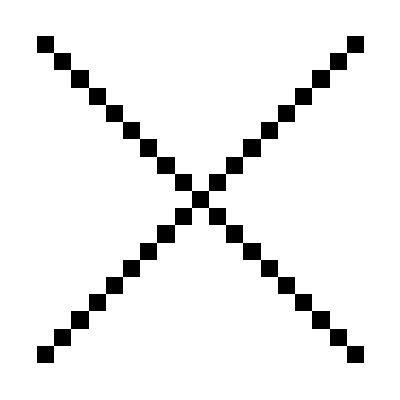

-Graphics-

```mathematica
tempf[m_,mp_,NN_]:=2/NN Chop@NSum[If[n==0,1/2,1]ChebyshevT[n,Cos[(π(m-1/2))/NN]]ChebyshevT[n,Cos[(π(mp-1/2))/NN]],{n,0,NN-1}]
tempf2[m_,mp_,NN_]:=2/NN Chop@NSum[If[n==0,1/2,1]Cos[n ((π(m-1/2))/NN)]Cos[n ((π(mp-1/2))/NN)],{n,0,NN-1}]
tempf2[m_,mp_,NN_]:=2/NN Chop@NSum[If[n==0,1/2,1]Cos[n ((π(m-1/2))/NN)]Cos[n ((π(mp-1/2))/NN)],{n,0,NN-1}]
ArrayPlot@With[{NN=10},Table[tempf[m,mp,NN],{m,Join[Range[-NN+1,-1],Range[1,NN]]},{mp,Join[Range[-NN+1,-1],Range[1,NN]]}]]
ArrayPlot@With[{NN=10},Table[tempf2[m,mp,NN],{m,Join[Range[-NN+1,-1],Range[1,NN]]},{mp,Join[Range[-NN+1,-1],Range[1,NN]]}]]
```

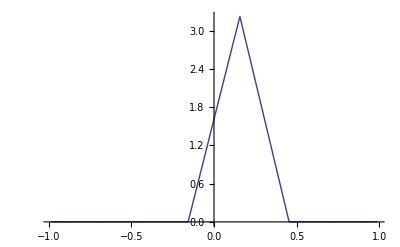

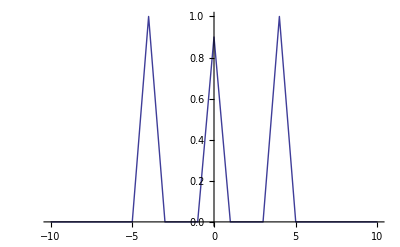

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-.5)/NN];
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))]
(*Δ[m_Integer,mp_Integer,NN_Integer]=2Sin[π/(2NN)]Sin[(Abs[m] π)/NN]*)
With[{NN=10,m=-5},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@DeleteCases[Range[-NN,NN],0]];
ListLinePlot[Sort@%, PlotRange->All]
tempf[m_Integer,mp_Integer,NN_Integer]:=2/NN Chop@NSum[If[n==0,1/2,1]ChebyshevT[n,Sign[m]Cos[(π(Abs@m-1/2))/NN]]ChebyshevT[n,Sign[m]Cos[(π(Abs@mp-1/2))/NN]],{n,0,NN-1}]
(*tempf[m_Integer,mp_Integer,NN_Integer]:=2/NN Chop@NSum[If[n==0,1/2,1]ChebyshevT[n,ϵmesh[m,NN]]ChebyshevT[n,ϵmesh[mp,NN]],{n,0,NN-1}]
*)With[{NN=10,m=-4},{#,tempf[#,m,NN]}&/@Range[-NN,NN]];
ListLinePlot[Sort@%, PlotRange->All]
```

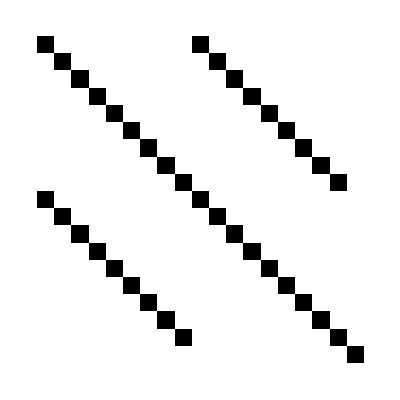

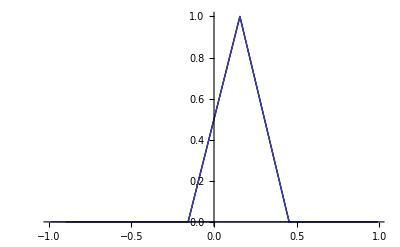

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-.5)/NN];
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;2/NN ch1.ch2 ]
ArrayPlot@With[{NN=10},Table[Chop@δKCh[m,mp,NN],{m,DeleteCases[Range[-NN+1,NN],0]},{mp,DeleteCases[Range[-NN+1,NN],0]}]]
ListLinePlot[With[{NN=10,m=-5},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@DeleteCases[Range[-NN,NN],0]],PlotRange->All]
```

#### Tests

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

NSum::emcon: Euler-Maclaurin sum failed to converge to requested error tolerance.

General::stop: Further output of NSum :: emcon will be suppressed during this calculation.

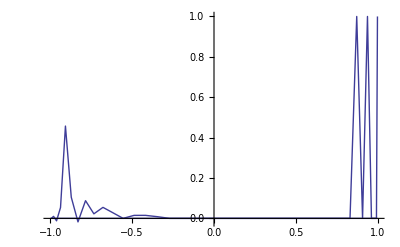

```mathematica
With[{NN=40,m=31},{ϵmesh[#,NN],tempf2[NN,m,#]}&/@Range[-NN,NN]];
ListLinePlot[%,PlotRange->All]
```

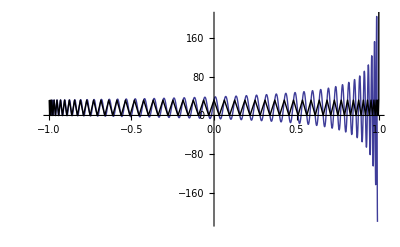

```mathematica
Clear@δCh2;
δCh2[ϵ_?NumericQ,n_Integer]:=(2./(π √(1-ϵ^2)))^-1 ChebyVec[ϵ,n-1].ChebyVec[Cos[π(1)/n],n-1] π/2
With[{n=100},Plot[δCh2[ϵ,n],{ϵ,-.99,.99}, PlotRange->All, Epilog->{Line[{#,δCh2[#,n]}&/@Most@Cos[π(Range[1,n-1])/n]]}]]
```

```mathematica
With[{NN=7,m=2,mp=2},{#,Total@#}&@Table[2./NN Cos[n ((2π)/NN m)]Cos[n ((2π)/NN mp)],{n,0,NN-1}]]
```

{{0.285714,0.0141473,0.231927,0.111068,0.111068,0.231927,0.0141473},1.}

```mathematica
With[{NN=10,m=2,mp=3},1/NN NSum[Exp[-ⅈ n ((2π)/NN m)]Exp[ⅈ n ((2π)/NN mp)],{n,0,NN-1}]]
```

-2.22045×10^-17-4.44089×10^-17 ⅈ

```mathematica
With[{NN=10,m=3,mp=4},NSum[Exp[-ⅈ n ((2π)/NN m)],{n,0,NN-1}]]
```

-2.60902×10^-15+1.33227×10^-15 ⅈ

## DOS

### Mayou DOS

#### Discussion

We wish to compute the DOS,  

	ρ(E)=Tr[δ(E-H)]≈⟨β|δ(E-H)|β⟩, 

where |β⟩ is a normalized random state. (One can also average over several random states to improve accuracy).

We will employ an expansion for the energy projector δ(E-H) in terms of Chebychev polynomials T_n(ϵ), defined in the interval [-1,1]. To this end, we write 

	H=ϵ_0+W h, 

where ϵ_0 and W are c-numbers, and h is an operator with eigenvalues contained in the interval [-1,1]. We will therefore expand  δ (E - H) = 1/W δ((E - ϵ_0)/W- h)=1/W δ(ϵ-h), where ϵ=(E - ϵ_0)/W is the dimensionless Fermi energy, also in the interval [-1,1]. We then have 
We use the spectral resolution of the identity:

	δ(ϵ-ϵ’)=∑_n 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 

where ν_0=2, ν_(n>0)=1 and N(ϵ)=2/π 1/(√(1-ϵ^2)). The T_n(ϵ) are orthogonal Chebychev polynomials, satsifying 1/ν_n∫_-1^1 dϵ T_n(ϵ)T_m(ϵ) N(ϵ)=δ_nm. The first two are T_0(ϵ)=1 and T_1(ϵ)=ϵ. They satisfy the recurrence

	T_(n+1)(ϵ)=2ϵ T_n(ϵ)-T_(n-1)(ϵ)
	
Using the above, we have a DOS of dimensionless energy ϵ:

	ρ(ϵ)=∑_n N(ϵ) T_n(ϵ)1/ν_n⟨β|T_n(h)|β⟩ 

The “DOS kernel” 1/ν_n⟨β|T_n(h)|β⟩ is computed efficiently by recursion, whereby T_(n+1)(h)|β⟩ =2 h T_n(h)|β⟩-T_(n-1)(h)|β⟩. After each iteration, one projects the resulting state back onto 1/ν_n⟨β|. In this way, only three states are kept in memory at any given time, |β⟩, T_n(h)|β⟩ and T_(n-1)(h)|β⟩.

Low energy projection:
If we wish information about the low energy DOS and the total bandwidth is large, then the resolution W/N might be poor for a reasonable value of N. We may then try to normalize h’=H/W’, where W’ is a smaller energy scale. This in itself doesn’t work, since the whole Chebyshev expasion fails if any eigenvalue of h’ is outside the [-1,1] window. However, we may try to project out the energy components of |β⟩ that lie outside this interval before doing the iterative Chebyshev expansion.
We therefore wish to compute θ(W'^2-H^2)|β⟩=P|β⟩, where θ is the Heaviside function. We once more use a Chebyshev expansion in h=H/W, so that P|β⟩=θ(w^2-h^2)|β⟩, where w=W’/W. This time, the expansion reads
	θ(w^2-ϵ^2) =∑_n^(even) 1/ν_n c_n(w)T_n(ϵ)
where c_n(w)=∫_-w^w dϵT_n(ϵ)=(T_(n+1)(w))/(n+1)-(T_(n-1)(w))/(n-1), where n is even and T_-1(w)=T_1(w)=w

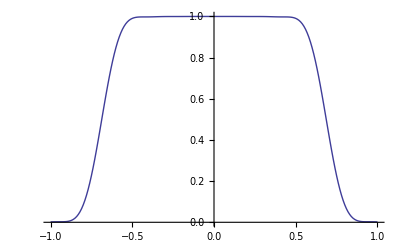

```mathematica
With[{w=.2,NN=120},
ListLinePlot[ChebyVec[(w+1/(√NN)) Range[-1,1,.01],NN].ThetaJackson[w,NN], DataRange->{-1,1}, PlotRange->{0,All}]]
```

#### Algorithm

```mathematica
Clear@DOSKernel;
Options[DOSKernel]={Samples->1,MaxChebyshev->10, UniformDensity->False, Bandwidth->1,BandFraction->1,Parallel->False, ProjectorOrder->40};
DOSKernel[H_SparseArray, opts:OptionsPattern[]]:=
(*DOSKernel[H,opts]=*)Module[{h,h0,β,hβ,dim=Length@H, kernel,ChebyshevRecursion},

If[N@OptionValue@Bandwidth≠1.,h0=H/N@OptionValue@Bandwidth,h0=H];
If[N@OptionValue@BandFraction≠1.,h=.8h0/(OptionValue@BandFraction+1/√(OptionValue@ProjectorOrder)),h=h0];
h=h0;

If[OptionValue@Parallel,ParallelTable,Table][

If[OptionValue@UniformDensity,β=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]],β=Normalize[RandomComplex[{-1-ⅈ,1+ⅈ},dim]]];

If[N@OptionValue@BandFraction≠1.,
β=ThetaJackson[OptionValue@BandFraction,OptionValue@ProjectorOrder].(Prepend[#[[All,2]],#[[1,1]]]&@NestList[{Last@#,2h0.Last@#-First@#}&,{β,h0.β},OptionValue@ProjectorOrder-1]);
];

kernel=First@Last@Reap@Nest[{temp=Last@#,((Sow[β*.#];#)&)[2h.Last@#-First@#]}&, ((Sow[β*.#];#)&)/@{β,h.β},OptionValue@MaxChebyshev-1];

kernel[[1]]=0.5;

Re@kernel,{OptionValue@Samples}]
]
```

```mathematica
ChebyVec=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];

DeltaJackson=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))((((nmax+2-#)Cos[(π#)/(nmax+2)]+Sin[(π#)/(nmax+2)]Cot[π/(nmax+2)])/(nmax+2)&)@Range[0,nmax])Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];
ThetaJackson[w_,nmax_]:=Module[{coeffs},coeffs=PadRight[Flatten[{#,0}&/@(#-Prepend[Rest@RotateRight[#],-w]&[1/Range[1,nmax,2](2./(π √(1-w^2)))^-1 DeltaJackson[w,nmax][[2;;;;2]]])],nmax+1];
coeffs[[1]]*=0.5;
coeffs]

ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]

DOS[kernel_List,OptionsPattern[{ChebyshevMesh->False,NumPoints->Automatic,UseFilter->False,Filter->1/4.{1,2,1}, JacksonKernel->True}]]:=Module[{ϵlist,Npoints,NN=Length@kernel-1, dos},
If[OptionValue@NumPoints===Automatic,Npoints=Length@kernel, Npoints=OptionValue@NumPoints];
If[OptionValue@ChebyshevMesh,ϵlist=ϵmesh[Npoints-1],ϵlist=Most@Rest@Range[-1,1,2/(Npoints+1)]];
If[OptionValue@JacksonKernel,dos=DeltaJackson[ϵlist,NN].kernel,dos=ChebyVec[ϵlist,NN].kernel];
If[OptionValue@UseFilter,dos=ListConvolve[OptionValue@Filter,dos,1]];
{ϵlist,dos}ᵀ]
```

#### Mayou DOS test

```mathematica
tempK=DOSKernel[H[0]/3,Samples->16,MaxChebyshev->200, Parallel->False, BandFraction->.9999, ProjectorOrder->80];//AbsoluteTiming
```

{5.119108,Null}

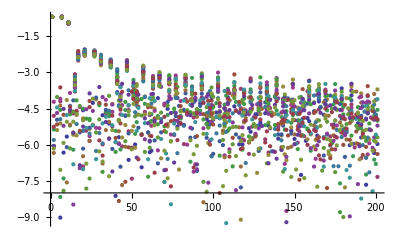

```mathematica
ListPlot@Log@tempK
```

```mathematica
SetDirectory@NotebookDirectory[];
<<"./DOSKernel-1024-1024-1.dat";
```

Get::noopen: Cannot open "./DOSKernel-1024-1024-1.dat".

```mathematica
MeanKernelDOS=Mean@tempK;
```

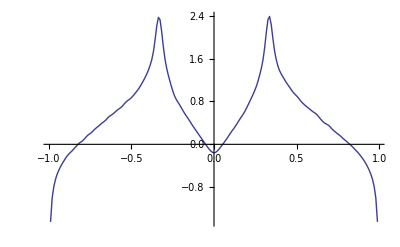

```mathematica
ListLinePlot[DOS[MeanKernelDOS]]
```

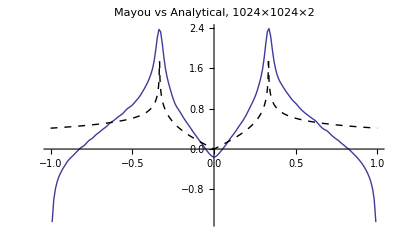

```mathematica
ListLinePlot[DOS[MeanKernelDOS], PlotRange->All];
Show[%,Plot[3/2 AnalyticDOS[3ϵ],{ϵ,-1,1},PlotStyle->{{Black,Dashed}}, PlotRange->All],PlotLabel->"Mayou vs Analytical, 1024×1024×2"]
```

## Conductivity

### Mayou’s Kubo algorithm

#### Discussion

We compute the Kubo dc conductivity σ_xx(ω), which is an integral 

	Re σ_xx(ω)=(2 e^2 ℏ)/Ω∫dE (f(E)-f(E+ℏω))/ℏω F(E,E')

of 

	F(E,E’) = Tr[V_x δ(E-H) V_x δ(E’-H)] ≈N/S∑_(p=1)^S ⟨β_p| V_x δ(E-H) V_x δ(E’-H) |β_p⟩, 

where V_x=-ⅈ[H,X] is the x-velocity, X is the x-position operator, H is the Hamiltonian, of size NxN, E is the Fermi energy, and |β_p⟩ are (normalized) random states (in large systems using only a single state [S=1] is enough).  This can be trivially generalized to Re σ_xy.

We will employ an expansion for the energy projectors δ(E-H) in terms of Chebychev polynomials T_n(ϵ), defined in the interval [-1,1]. To this end, we write 

	H=ϵ_0+W h, 
	
where ϵ_0 and W are c-numbers, and h is an operator with eigenvalues contained in the interval [-1,1]. We will therefore expand  δ (E - H) = 1/W δ((E - ϵ_0)/W- h)=1/W δ(ϵ-h), where ϵ=(E - ϵ_0)/W is the dimensionless Fermi energy, also in the interval [-1,1]. We then have 

	F(ϵ,ϵ') = ⟨β| v_x δ(ϵ-h) v_x δ(ϵ’-h) |β⟩  

where v_x=-ⅈ[h,X]=V_x/W. (The W factors cancel).

We use the spectral resolution of the identity:

	δ(ϵ-ϵ’)=∑_n 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 
	
where ν_0=2, ν_(n>0)=1 and N(ϵ)=2/π 1/(√(1-ϵ^2)). The T_n(ϵ) are orthogonal Chebychev polynomials, satsifying 1/ν_n∫_-1^1 dϵ T_n(ϵ)T_m(ϵ) N(ϵ)=δ_nm. The first two are T_0(ϵ)=1 and T_1(ϵ)=ϵ. They satisfy the recurrence

	T_(n+1)(ϵ)=2ϵ T_n(ϵ)-T_(n-1)(ϵ)
	
Using the above, we can write F(ϵ,ϵ’) 

	F (ϵ, ϵ') = ∑_nm 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x T_m(h)|β⟩T_n(ϵ) T_m(ϵ')

in terms of the “Kubo Kernel” 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x T_m(h)|β⟩

A practical way to compute the Kubo Kernel is a two step recursion, whereby we first compute (and store) the bras 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x, (for n=0,... nmax) using T_m(h) recursion, and then do a second recursion for T_m(h)|β⟩, in which we only store two states at any given time, like for the DOS. In the second recursion cycle we project onto the 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x bras at each step, “sowing” the results along the way, which are “reaped” only at the end for numerical efficiency.

Regarding the exact coefficient of σ, Kubo says:

	σ(ω)=-ⅈ g(e^2 ℏ)/(ℏω A)∑_nm (f(E_m)-f(E_n))/(ℏω-E_m+E_n+ⅈ0)⟨m|v|n⟩⟨n|v|m⟩
	Re[σ(ω)]=g(π e^2 ℏ)/A∑_nm (f(E_m)-f(E_n))/(ℏ ω)δ(ℏω-E_m+E_n)⟨m|v|n⟩⟨n|v|m⟩ =g(π e^2 ℏ)/A∫dE (f(E)-f(E+ℏω))/(ℏ ω)Tr[v δ(E-H) v δ(E+ℏω-H)]=g(π e^2 ℏ)/(W^2 A/N)∫dϵ (f(ϵ)-f(ϵ+ℏω/W))/(ℏ ω/W)F(ϵ,ϵ+ℏω/W)=g (π e^2 ℏ)/(W^2 A/N)∫dϵ (f(ϵ)-f(ϵ+ℏω/W))/(ℏ ω/W)F(ϵ,ϵ+ℏω/W)=(2 π^2 g ℏ^2)/(W^2 A/N) e^2/h∫dϵ (f(ϵ)-f(ϵ+ℏω/W))/(ℏ ω/W)F(ϵ,ϵ+ℏω/W)
	
Here, g is the degeneracy of each normalized state |n⟩ (often g=g_s=2), while A is the area of the system, and A/N is the area per site of the lattice. In the last expression, Fermi functions are evaluated for dimensionless temperature K_B t=K_B T/W

Optimal meshing of integrals
We recall that, for an expansion of order N, the optimal energy mesh should be the zeroes of T_(N+1). This gives the best resolution of the Delta function.
When evalating σ, we should actually compute F(ϵ_m,ϵ_m'). The integral would then be computed as a sum. The problem with this approach is that if ϵ_m belongs to the optimal mesh, then ϵ_m+ℏω/W will not. An option is the use the mesh to build an interpolation function F(ϵ,ϵ’) for all ϵ, ϵ’. In this case, linear interpolation will work best, since there will be zero overshoot in delta-like features

#### Algorithm

```mathematica
Clear@KuboKernel;
Options[KuboKernel]={Samples->1,MaxChebyshev->100, UniformDensity->True, Parallel->False};
KuboKernel[h_SparseArray,v_SparseArray, opts:OptionsPattern[]]:=
KuboKernel[h,v, opts]=Module[{β,βv,βvTv, dim=Length@h, w,ChebyshevRecursion},

(*ChebyshevRecursion[{βa_, βb_}]:={βb,2h.βb-βa};*)

If[OptionValue@Parallel,ParallelTable,Table][
Clear[βvTv,βv,β,w];
If[OptionValue@UniformDensity,β=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]],β=Normalize[RandomComplex[{-1-ⅈ,1+ⅈ},dim]]];

βv=β*.v;

(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];))*);
(*βvTv=(Prepend[Last[#].v&/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv.v])*);
(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];));*)
(*βvTv=(Prepend[Last/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv].v)*);

βvTv=(First@Last@Reap@(Nest[{Last@#,Sow[2Last@#.h-First@#]}&,Sow/@{βv,βv.h},OptionValue@MaxChebyshev-1];).v);

w=First@Last@Reap@(Nest[{Last@#,(Sow[βvTv.#];#)&[2h.Last@#-First@#]}&,(Sow[βvTv.#];#)&/@{β,h.β},OptionValue@MaxChebyshev-1];); 
(*w=Join[{βvTv.β},#[[2,1]],{βvTv.#[[1,2]]}]&@Reap@Nest[ChebyshevRecursion[Sow[βvTv.Last@#];#]&,{β,h.β},OptionValue@MaxChebyshev-1]*);

w[[All,1]]*=0.5;w[[1,All]]*=0.5;(*This includes the weight Subscript[ν, n] into the polynomials Subscript[T, n][h]*)
Re@((w+w†)/2),{OptionValue@Samples}] (*The Re@(w+w†)/2 enforcement is unnecessary when averaging over many β (trace property)*)
]
```

```mathematica
Clear@ChebyVec;
ChebyVec=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];
DeltaJackson=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))((((nmax+2-#)Cos[(π#)/(nmax+2)]+Sin[(π#)/(nmax+2)]Cot[π/(nmax+2)])/(nmax+2)&)@Range[0,nmax])Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];

ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]
(*ϵmesh[NN_]:=.99Sort@Range[-1,1,1/Round[NN/π]]*)

KuboσF[kernel_List, OptionsPattern[{ChebyshevMesh->False,NumPoints->Automatic,UseFilter->False,Filter->1/8.({{0, 1, 0}, {1, 4, 1}, {0, 1, 0}}), JacksonKernel->True,InterpolationOrder->1}]]:=Module[{ϵlist,delta,NN=Length@kernel-1,Npoints,F,ϵϵ, data},
If[OptionValue@NumPoints===Automatic,Npoints=Length@kernel, Npoints=OptionValue@NumPoints];
If[OptionValue@ChebyshevMesh,ϵlist=ϵmesh[Npoints-1],ϵlist=Most@Rest@Range[-1,1,2/(Npoints+1)]];
If[OptionValue@JacksonKernel,delta=DeltaJackson[ϵlist, NN],delta=ChebyVec[ϵlist, NN]];
F=delta.kernel.deltaᵀ;
(*If[OptionValue@SuppressDrudePeak,Table[F[[i,i]]=0.,{i,1,Length[F]}]];*)
If[OptionValue@UseFilter,F=ListConvolve[OptionValue@Filter,F,1]];
ϵϵ=Outer[List,ϵlist,ϵlist];
data=MapThread[Append,{ϵϵ,F},2];
temp=data[[All,All,3]];
Interpolation[Flatten[data,1], InterpolationOrder->OptionValue@InterpolationOrder]];
```

#### Mayou Kubo Tests

```mathematica
CloseKernels[];LaunchKernels[3];
```

```mathematica
tempK=KuboKernel[H[0]/3,vx/1.5,MaxChebyshev->nmax, Samples->64, Parallel->False];//AbsoluteTiming
(*ArrayPlot[tempK, PlotRange->All]*)
```

{30.06027,Null}

```mathematica
SetDirectory@NotebookDirectory[];
<<"../KuboKernel-600-600-64.dat";
tempK600=tempK;
nmax=600;
```

Get::noopen: Cannot open "../KuboKernel-600-600-64.dat".

```mathematica
SetDirectory@NotebookDirectory[];
<<"../KuboKernel-300-300-64.dat";
tempK300=tempK;
nmax=300;
```

Get::noopen: Cannot open "../KuboKernel-300-300-64.dat".

```mathematica
MeanKernel=Mean@tempK300;
Dimensions@%
```

{101,101}

```mathematica
Clear@tempi
tempi=KuboσF[MeanKernel,JacksonKernel->False,ChebyshevMesh->True,UseFilter->True,InterpolationOrder->1]
f[ω_]:=1/(1+ⅇ^ω)
Clear@σ;
σ[ϵF_, ω_, T_:0.000001]:=(2π)^2/((3 √3)/2/2)1.5^2/3^2 NIntegrate[(f[(ϵ-ϵF)/T]-f[(ϵ-ϵF+ω)/T])/ω tempi[ϵ,ϵ+ω],{ϵ,ϵF-Max[ω,0]-3T,ϵF+Max[-ω,0]+3T}]
```

InterpolatingFunction[{{-0.999879,0.999879},{-0.999879,0.999879}},<>]

```mathematica
Clear@tempi
tempi=KuboσF[MeanKernel]
f[ω_]:=1/(1+ⅇ^ω)
Clear@σ;
σ[ϵF_, ω_, T_:0.000001]:=(2π)^2/((3 √3)/2/2)1.5^2/3^2 NIntegrate[(f[(ϵ-ϵF)/T]-f[(ϵ-ϵF+ω)/T])/ω tempi[ϵ,ϵ+ω],{ϵ,ϵF-Max[ω,0]-3T,ϵF+Max[-ω,0]+3T}]
```

InterpolatingFunction[{{-0.980392,0.980392},{-0.980392,0.980392}},<>]

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-.1001,.1,(.2)/90]]; 
ListLinePlot[{tempp,temppold}, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

ListLinePlot::lpn: {{{-0.1001, 1.06705}, {-0.0978778, 1.07222}, {-0.0956556, 1.07774}, {-0.0934333, 1.08334}, {-0.0912111, 1.08906}, « 42 », {0.00434444, 1.31753}, {0.00656667, 1.31452}, {0.00878889, 1.31186}, « 41 »}, temppold} is not a list of numbers or pairs of numbers.

ListLinePlot[{{{-0.1001,1.06705},{-0.0978778,1.07222},{-0.0956556,1.07774},{-0.0934333,1.08334},{-0.0912111,1.08906},{-0.0889889,1.09496},{-0.0867667,1.10109},{-0.0845444,1.10752},{-0.0823222,1.11432},{-0.0801,1.12156},{-0.0778778,1.12933},{-0.0756556,1.13733},{-0.0734333,1.14542},{-0.0712111,1.15357},{-0.0689889,1.16173},{-0.0667667,1.16988},{-0.0645444,1.17797},{-0.0623222,1.18594},{-0.0601,1.19373},{-0.0578778,1.20134},{-0.0556556,1.20914},{-0.0534333,1.21712},{-0.0512111,1.22516},{-0.0489889,1.23313},{-0.0467667,1.24087},{-0.0445444,1.24817},{-0.0423222,1.25481},{-0.0401,1.26048},{-0.0378778,1.26518},{-0.0356556,1.27014},{-0.0334333,1.2754},{-0.0312111,1.28084},{-0.0289889,1.28631},{-0.0267667,1.2916},{-0.0245444,1.29643},{-0.0223222,1.3004},{-0.0201,1.30286},{-0.0178778,1.30415},{-0.0156556,1.30559},{-0.0134333,1.30731},{-0.0112111,1.30932},{-0.00898889,1.31164},{-0.00676667,1.31427},{-0.00454444,1.31724},{-0.00232222,1.32074},{-0.0001,1.32215},{0.00212222,1.32111},{0.00434444,1.31753},{0.00656667,1.31452},{0.00878889,1.31186},{0.0110111,1.30952},{0.0132333,1.30748},{0.0154556,1.30573},{0.0176778,1.30427},{0.0199,1.30299},{0.0221222,1.3007},{0.0243444,1.29682},{0.0265667,1.29205},{0.0287889,1.28679},{0.0310111,1.28133},{0.0332333,1.27588},{0.0354556,1.2706},{0.0376778,1.26562},{0.0399,1.26089},{0.0421222,1.25536},{0.0443444,1.2488},{0.0465667,1.24155},{0.0487889,1.23384},{0.0510111,1.22588},{0.0532333,1.21784},{0.0554556,1.20985},{0.0576778,1.20204},{0.0599,1.19442},{0.0621222,1.18665},{0.0643444,1.17869},{0.0665667,1.17061},{0.0687889,1.16247},{0.0710111,1.1543},{0.0732333,1.14615},{0.0754556,1.13806},{0.0776778,1.13004},{0.0799,1.12224},{0.0821222,1.11495},{0.0843444,1.10812},{0.0865667,1.10166},{0.0887889,1.0955},{0.0910111,1.08958},{0.0932333,1.08385},{0.0954556,1.07824},{0.0976778,1.07272},{0.0999,1.06748}},temppold},PlotRange→{0,All},PlotRange→All,PlotRangePadding→None,Frame→True,FrameLabel→{ω/W,σ(ω)[π/2e^2/h]},BaseStyle→FontSize→15,PlotLabel→σ(ω), no disorder, 600x600x2 site graphene,Epilog→{Dashing[{Small,Small}],Line[{{0,1},{1,1}}]}]

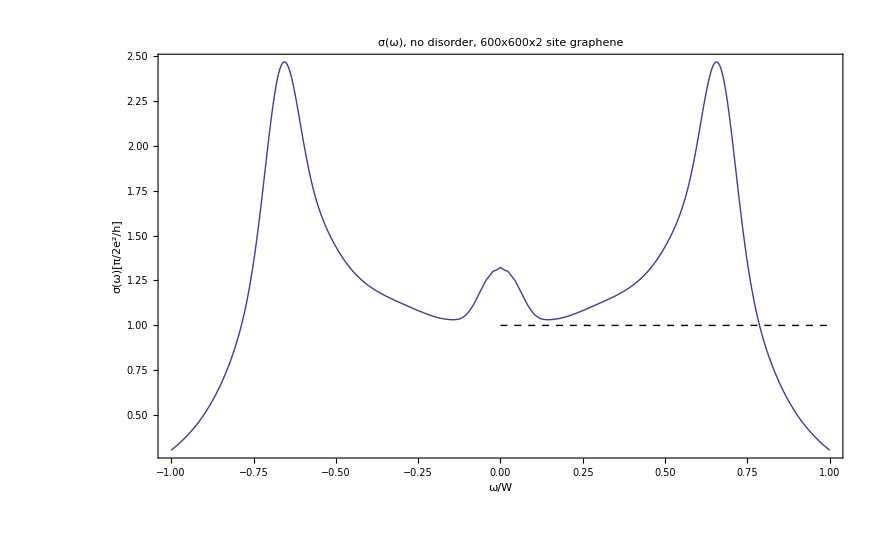

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-1,1,2./601]]; 
ListLinePlot[tempp, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

#### PETSC kernel Tests

```mathematica
SetDirectory@NotebookDirectory[];
MeanKernel0=Import["dat_MkII_8_part.dat"];
MeanKernel=Partition[MeanKernel0[[All,1]]+ⅈ MeanKernel0[[All,2]],600];
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Partition[MeanKernel0[[All,2]],600];
Max@Abs[%-%ᵀ]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Abs[Symbol[]-Transpose[Symbol[]]]

```mathematica
SetDirectory@NotebookDirectory[];
MeanKernel=Import["DAT_64_averaged.dat"];
```

Import::nffil: File not found during Import.

```mathematica
Im@MeanKernel;
Max[%-%†]
```

-ConjugateTranspose[Im[$Failed]]+Im[$Failed]

```mathematica
Clear@tempi
tempi=KuboσF[MeanKernel]
f[ω_]:=1/(1+ⅇ^ω)
Clear@σ;
σ[ϵF_, ω_, T_:0.000001]:=(2π)^2/((3 √3)/2/2)1/3.1^2 NIntegrate[(f[(ϵ-ϵF)/T]-f[(ϵ-ϵF+ω)/T])/ω tempi[ϵ,ϵ+ω],{ϵ,ϵF-Max[ω,0]-3T,ϵF+Max[-ω,0]+3T}]
```

KuboσF[$Failed]

```mathematica
σ[0.,.2]
```

NIntegrate::inumr: The integrand 5.\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.2  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.200003, 3.×10^-6}}.

3.16238 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.2)/(1.×10^-6)]) tempi[ϵ,ϵ+0.2])/0.2,{ϵ,0.-Max[0.2,0]-3 1.×10^-6,0.+Max[-0.2,0]+3 1.×10^-6}]

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-.1001,.1,(.2)/90]]; 
ListLinePlot[{tempp,temppold}, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

NIntegrate::inumr: The integrand -9.99001\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.1001 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.100103}}.

NIntegrate::inumr: The integrand -12.1474\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0823222 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0823252}}.

NIntegrate::inumr: The integrand -15.4932\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0645444 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0645474}}.

NIntegrate::inumr: The integrand -9.99001\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.1001 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.100103}}.

NIntegrate::inumr: The integrand -12.1474\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0823222 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0823252}}.

NIntegrate::inumr: The integrand -15.4932\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0645444 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0645474}}.

NIntegrate::inumr: The integrand -9.99001\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.1001 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.100103}}.

NIntegrate::inumr: The integrand -12.1474\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0823222 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0823252}}.

NIntegrate::inumr: The integrand -15.4932\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0645444 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0645474}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -21.3828\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0467667 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0467697}}.

NIntegrate::inumr: The integrand -34.496\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0289889 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0289919}}.

NIntegrate::inumr: The integrand -21.3828\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0467667 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0467697}}.

NIntegrate::inumr: The integrand -34.496\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0289889 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0289919}}.

NIntegrate::inumr: The integrand -21.3828\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0467667 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0467697}}.

NIntegrate::inumr: The integrand -34.496\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0289889 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0289919}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -89.1972\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0112111 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0112141}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 152.284\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.00656667  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.00656967, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 41.0771\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0243444  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0243474, 3.×10^-6}}.

NIntegrate::inumr: The integrand 25.0627\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0399  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.039903, 3.×10^-6}}.

NIntegrate::inumr: The integrand 41.0771\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0243444  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0243474, 3.×10^-6}}.

NIntegrate::inumr: The integrand 25.0627\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0399  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.039903, 3.×10^-6}}.

NIntegrate::inumr: The integrand 41.0771\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0243444  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0243474, 3.×10^-6}}.

NIntegrate::inumr: The integrand 25.0627\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0399  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.039903, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 18.0325\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0554556  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0554586, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 14.0823\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0710111  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0710141, 3.×10^-6}}.

NIntegrate::inumr: The integrand 11.5518\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0865667  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0865697, 3.×10^-6}}.

NIntegrate::inumr: The integrand 14.0823\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0710111  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0710141, 3.×10^-6}}.

NIntegrate::inumr: The integrand 11.5518\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0865667  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0865697, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 11.5518\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.0865667  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.0865697, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -9.99001\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.1001 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.100103}}.

NIntegrate::inumr: The integrand -10.2168\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0978778 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0978808}}.

NIntegrate::inumr: The integrand -10.4542\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0956556 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0956586}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -9.99001\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.1001 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.100103}}.

NIntegrate::inumr: The integrand -10.2168\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0978778 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0978808}}.

NIntegrate::inumr: The integrand -10.4542\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0956556 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0956586}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

ListLinePlot::lpn: {{{-0.1001, 2.01324\ NIntegrate[(Plus[« 2 »]\ Power[« 2 »])\ tempi[ϵ, Plus[« 2 »]], {ϵ, 0.  + Times[« 2 »] + Times[« 2 »], 0.  + Max[« 2 »] + Times[« 2 »]}]}, {-0.0978778, 2.01324\ NIntegrate[(Plus[« 2 »]\ Power[« 2 »])\ tempi[ϵ, Plus[« 2 »]], {ϵ, 0.  + Times[« 2 »] + Times[« 2 »], 0.  + Max[« 2 »] + Times[« 2 »]}]}, « 48 », « 41 »}, temppold}
 is not a list of numbers or pairs of numbers.

ListLinePlot[{{{-0.1001,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.1001)/(1.×10^-6)]) tempi[ϵ,ϵ-0.1001])/0.1001,{ϵ,0.-Max[-0.1001,0]-3 1.×10^-6,0.+Max[-(-0.1001),0]+3 1.×10^-6}]},{-0.0978778,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0978778)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0978778])/0.0978778,{ϵ,0.-Max[-0.0978778,0]-3 1.×10^-6,0.+Max[-(-0.0978778),0]+3 1.×10^-6}]},{-0.0956556,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0956556)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0956556])/0.0956556,{ϵ,0.-Max[-0.0956556,0]-3 1.×10^-6,0.+Max[-(-0.0956556),0]+3 1.×10^-6}]},{-0.0934333,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0934333)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0934333])/0.0934333,{ϵ,0.-Max[-0.0934333,0]-3 1.×10^-6,0.+Max[-(-0.0934333),0]+3 1.×10^-6}]},{-0.0912111,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0912111)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0912111])/0.0912111,{ϵ,0.-Max[-0.0912111,0]-3 1.×10^-6,0.+Max[-(-0.0912111),0]+3 1.×10^-6}]},{-0.0889889,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0889889)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0889889])/0.0889889,{ϵ,0.-Max[-0.0889889,0]-3 1.×10^-6,0.+Max[-(-0.0889889),0]+3 1.×10^-6}]},{-0.0867667,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0867667)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0867667])/0.0867667,{ϵ,0.-Max[-0.0867667,0]-3 1.×10^-6,0.+Max[-(-0.0867667),0]+3 1.×10^-6}]},{-0.0845444,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0845444)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0845444])/0.0845444,{ϵ,0.-Max[-0.0845444,0]-3 1.×10^-6,0.+Max[-(-0.0845444),0]+3 1.×10^-6}]},{-0.0823222,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0823222)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0823222])/0.0823222,{ϵ,0.-Max[-0.0823222,0]-3 1.×10^-6,0.+Max[-(-0.0823222),0]+3 1.×10^-6}]},{-0.0801,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0801)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0801])/0.0801,{ϵ,0.-Max[-0.0801,0]-3 1.×10^-6,0.+Max[-(-0.0801),0]+3 1.×10^-6}]},{-0.0778778,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0778778)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0778778])/0.0778778,{ϵ,0.-Max[-0.0778778,0]-3 1.×10^-6,0.+Max[-(-0.0778778),0]+3 1.×10^-6}]},{-0.0756556,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0756556)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0756556])/0.0756556,{ϵ,0.-Max[-0.0756556,0]-3 1.×10^-6,0.+Max[-(-0.0756556),0]+3 1.×10^-6}]},{-0.0734333,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0734333)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0734333])/0.0734333,{ϵ,0.-Max[-0.0734333,0]-3 1.×10^-6,0.+Max[-(-0.0734333),0]+3 1.×10^-6}]},{-0.0712111,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0712111)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0712111])/0.0712111,{ϵ,0.-Max[-0.0712111,0]-3 1.×10^-6,0.+Max[-(-0.0712111),0]+3 1.×10^-6}]},{-0.0689889,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0689889)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0689889])/0.0689889,{ϵ,0.-Max[-0.0689889,0]-3 1.×10^-6,0.+Max[-(-0.0689889),0]+3 1.×10^-6}]},{-0.0667667,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0667667)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0667667])/0.0667667,{ϵ,0.-Max[-0.0667667,0]-3 1.×10^-6,0.+Max[-(-0.0667667),0]+3 1.×10^-6}]},{-0.0645444,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0645444)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0645444])/0.0645444,{ϵ,0.-Max[-0.0645444,0]-3 1.×10^-6,0.+Max[-(-0.0645444),0]+3 1.×10^-6}]},{-0.0623222,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0623222)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0623222])/0.0623222,{ϵ,0.-Max[-0.0623222,0]-3 1.×10^-6,0.+Max[-(-0.0623222),0]+3 1.×10^-6}]},{-0.0601,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0601)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0601])/0.0601,{ϵ,0.-Max[-0.0601,0]-3 1.×10^-6,0.+Max[-(-0.0601),0]+3 1.×10^-6}]},{-0.0578778,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0578778)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0578778])/0.0578778,{ϵ,0.-Max[-0.0578778,0]-3 1.×10^-6,0.+Max[-(-0.0578778),0]+3 1.×10^-6}]},{-0.0556556,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0556556)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0556556])/0.0556556,{ϵ,0.-Max[-0.0556556,0]-3 1.×10^-6,0.+Max[-(-0.0556556),0]+3 1.×10^-6}]},{-0.0534333,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0534333)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0534333])/0.0534333,{ϵ,0.-Max[-0.0534333,0]-3 1.×10^-6,0.+Max[-(-0.0534333),0]+3 1.×10^-6}]},{-0.0512111,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0512111)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0512111])/0.0512111,{ϵ,0.-Max[-0.0512111,0]-3 1.×10^-6,0.+Max[-(-0.0512111),0]+3 1.×10^-6}]},{-0.0489889,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0489889)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0489889])/0.0489889,{ϵ,0.-Max[-0.0489889,0]-3 1.×10^-6,0.+Max[-(-0.0489889),0]+3 1.×10^-6}]},{-0.0467667,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0467667)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0467667])/0.0467667,{ϵ,0.-Max[-0.0467667,0]-3 1.×10^-6,0.+Max[-(-0.0467667),0]+3 1.×10^-6}]},{-0.0445444,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0445444)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0445444])/0.0445444,{ϵ,0.-Max[-0.0445444,0]-3 1.×10^-6,0.+Max[-(-0.0445444),0]+3 1.×10^-6}]},{-0.0423222,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0423222)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0423222])/0.0423222,{ϵ,0.-Max[-0.0423222,0]-3 1.×10^-6,0.+Max[-(-0.0423222),0]+3 1.×10^-6}]},{-0.0401,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0401)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0401])/0.0401,{ϵ,0.-Max[-0.0401,0]-3 1.×10^-6,0.+Max[-(-0.0401),0]+3 1.×10^-6}]},{-0.0378778,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0378778)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0378778])/0.0378778,{ϵ,0.-Max[-0.0378778,0]-3 1.×10^-6,0.+Max[-(-0.0378778),0]+3 1.×10^-6}]},{-0.0356556,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0356556)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0356556])/0.0356556,{ϵ,0.-Max[-0.0356556,0]-3 1.×10^-6,0.+Max[-(-0.0356556),0]+3 1.×10^-6}]},{-0.0334333,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0334333)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0334333])/0.0334333,{ϵ,0.-Max[-0.0334333,0]-3 1.×10^-6,0.+Max[-(-0.0334333),0]+3 1.×10^-6}]},{-0.0312111,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0312111)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0312111])/0.0312111,{ϵ,0.-Max[-0.0312111,0]-3 1.×10^-6,0.+Max[-(-0.0312111),0]+3 1.×10^-6}]},{-0.0289889,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0289889)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0289889])/0.0289889,{ϵ,0.-Max[-0.0289889,0]-3 1.×10^-6,0.+Max[-(-0.0289889),0]+3 1.×10^-6}]},{-0.0267667,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0267667)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0267667])/0.0267667,{ϵ,0.-Max[-0.0267667,0]-3 1.×10^-6,0.+Max[-(-0.0267667),0]+3 1.×10^-6}]},{-0.0245444,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0245444)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0245444])/0.0245444,{ϵ,0.-Max[-0.0245444,0]-3 1.×10^-6,0.+Max[-(-0.0245444),0]+3 1.×10^-6}]},{-0.0223222,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0223222)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0223222])/0.0223222,{ϵ,0.-Max[-0.0223222,0]-3 1.×10^-6,0.+Max[-(-0.0223222),0]+3 1.×10^-6}]},{-0.0201,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0201)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0201])/0.0201,{ϵ,0.-Max[-0.0201,0]-3 1.×10^-6,0.+Max[-(-0.0201),0]+3 1.×10^-6}]},{-0.0178778,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0178778)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0178778])/0.0178778,{ϵ,0.-Max[-0.0178778,0]-3 1.×10^-6,0.+Max[-(-0.0178778),0]+3 1.×10^-6}]},{-0.0156556,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0156556)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0156556])/0.0156556,{ϵ,0.-Max[-0.0156556,0]-3 1.×10^-6,0.+Max[-(-0.0156556),0]+3 1.×10^-6}]},{-0.0134333,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0134333)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0134333])/0.0134333,{ϵ,0.-Max[-0.0134333,0]-3 1.×10^-6,0.+Max[-(-0.0134333),0]+3 1.×10^-6}]},{-0.0112111,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0112111)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0112111])/0.0112111,{ϵ,0.-Max[-0.0112111,0]-3 1.×10^-6,0.+Max[-(-0.0112111),0]+3 1.×10^-6}]},{-0.00898889,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.00898889)/(1.×10^-6)]) tempi[ϵ,ϵ-0.00898889])/0.00898889,{ϵ,0.-Max[-0.00898889,0]-3 1.×10^-6,0.+Max[-(-0.00898889),0]+3 1.×10^-6}]},{-0.00676667,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.00676667)/(1.×10^-6)]) tempi[ϵ,ϵ-0.00676667])/0.00676667,{ϵ,0.-Max[-0.00676667,0]-3 1.×10^-6,0.+Max[-(-0.00676667),0]+3 1.×10^-6}]},{-0.00454444,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.00454444)/(1.×10^-6)]) tempi[ϵ,ϵ-0.00454444])/0.00454444,{ϵ,0.-Max[-0.00454444,0]-3 1.×10^-6,0.+Max[-(-0.00454444),0]+3 1.×10^-6}]},{-0.00232222,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.00232222)/(1.×10^-6)]) tempi[ϵ,ϵ-0.00232222])/0.00232222,{ϵ,0.-Max[-0.00232222,0]-3 1.×10^-6,0.+Max[-(-0.00232222),0]+3 1.×10^-6}]},{-0.0001,2.01324 NIntegrate[-((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.-0.0001)/(1.×10^-6)]) tempi[ϵ,ϵ-0.0001])/0.0001,{ϵ,0.-Max[-0.0001,0]-3 1.×10^-6,0.+Max[-(-0.0001),0]+3 1.×10^-6}]},{0.00212222,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.00212222)/(1.×10^-6)]) tempi[ϵ,ϵ+0.00212222])/0.00212222,{ϵ,0.-Max[0.00212222,0]-3 1.×10^-6,0.+Max[-0.00212222,0]+3 1.×10^-6}]},{0.00434444,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.00434444)/(1.×10^-6)]) tempi[ϵ,ϵ+0.00434444])/0.00434444,{ϵ,0.-Max[0.00434444,0]-3 1.×10^-6,0.+Max[-0.00434444,0]+3 1.×10^-6}]},{0.00656667,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.00656667)/(1.×10^-6)]) tempi[ϵ,ϵ+0.00656667])/0.00656667,{ϵ,0.-Max[0.00656667,0]-3 1.×10^-6,0.+Max[-0.00656667,0]+3 1.×10^-6}]},{0.00878889,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.00878889)/(1.×10^-6)]) tempi[ϵ,ϵ+0.00878889])/0.00878889,{ϵ,0.-Max[0.00878889,0]-3 1.×10^-6,0.+Max[-0.00878889,0]+3 1.×10^-6}]},{0.0110111,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0110111)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0110111])/0.0110111,{ϵ,0.-Max[0.0110111,0]-3 1.×10^-6,0.+Max[-0.0110111,0]+3 1.×10^-6}]},{0.0132333,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0132333)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0132333])/0.0132333,{ϵ,0.-Max[0.0132333,0]-3 1.×10^-6,0.+Max[-0.0132333,0]+3 1.×10^-6}]},{0.0154556,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0154556)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0154556])/0.0154556,{ϵ,0.-Max[0.0154556,0]-3 1.×10^-6,0.+Max[-0.0154556,0]+3 1.×10^-6}]},{0.0176778,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0176778)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0176778])/0.0176778,{ϵ,0.-Max[0.0176778,0]-3 1.×10^-6,0.+Max[-0.0176778,0]+3 1.×10^-6}]},{0.0199,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0199)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0199])/0.0199,{ϵ,0.-Max[0.0199,0]-3 1.×10^-6,0.+Max[-0.0199,0]+3 1.×10^-6}]},{0.0221222,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0221222)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0221222])/0.0221222,{ϵ,0.-Max[0.0221222,0]-3 1.×10^-6,0.+Max[-0.0221222,0]+3 1.×10^-6}]},{0.0243444,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0243444)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0243444])/0.0243444,{ϵ,0.-Max[0.0243444,0]-3 1.×10^-6,0.+Max[-0.0243444,0]+3 1.×10^-6}]},{0.0265667,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0265667)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0265667])/0.0265667,{ϵ,0.-Max[0.0265667,0]-3 1.×10^-6,0.+Max[-0.0265667,0]+3 1.×10^-6}]},{0.0287889,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0287889)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0287889])/0.0287889,{ϵ,0.-Max[0.0287889,0]-3 1.×10^-6,0.+Max[-0.0287889,0]+3 1.×10^-6}]},{0.0310111,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0310111)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0310111])/0.0310111,{ϵ,0.-Max[0.0310111,0]-3 1.×10^-6,0.+Max[-0.0310111,0]+3 1.×10^-6}]},{0.0332333,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0332333)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0332333])/0.0332333,{ϵ,0.-Max[0.0332333,0]-3 1.×10^-6,0.+Max[-0.0332333,0]+3 1.×10^-6}]},{0.0354556,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0354556)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0354556])/0.0354556,{ϵ,0.-Max[0.0354556,0]-3 1.×10^-6,0.+Max[-0.0354556,0]+3 1.×10^-6}]},{0.0376778,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0376778)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0376778])/0.0376778,{ϵ,0.-Max[0.0376778,0]-3 1.×10^-6,0.+Max[-0.0376778,0]+3 1.×10^-6}]},{0.0399,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0399)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0399])/0.0399,{ϵ,0.-Max[0.0399,0]-3 1.×10^-6,0.+Max[-0.0399,0]+3 1.×10^-6}]},{0.0421222,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0421222)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0421222])/0.0421222,{ϵ,0.-Max[0.0421222,0]-3 1.×10^-6,0.+Max[-0.0421222,0]+3 1.×10^-6}]},{0.0443444,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0443444)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0443444])/0.0443444,{ϵ,0.-Max[0.0443444,0]-3 1.×10^-6,0.+Max[-0.0443444,0]+3 1.×10^-6}]},{0.0465667,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0465667)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0465667])/0.0465667,{ϵ,0.-Max[0.0465667,0]-3 1.×10^-6,0.+Max[-0.0465667,0]+3 1.×10^-6}]},{0.0487889,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0487889)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0487889])/0.0487889,{ϵ,0.-Max[0.0487889,0]-3 1.×10^-6,0.+Max[-0.0487889,0]+3 1.×10^-6}]},{0.0510111,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0510111)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0510111])/0.0510111,{ϵ,0.-Max[0.0510111,0]-3 1.×10^-6,0.+Max[-0.0510111,0]+3 1.×10^-6}]},{0.0532333,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0532333)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0532333])/0.0532333,{ϵ,0.-Max[0.0532333,0]-3 1.×10^-6,0.+Max[-0.0532333,0]+3 1.×10^-6}]},{0.0554556,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0554556)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0554556])/0.0554556,{ϵ,0.-Max[0.0554556,0]-3 1.×10^-6,0.+Max[-0.0554556,0]+3 1.×10^-6}]},{0.0576778,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0576778)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0576778])/0.0576778,{ϵ,0.-Max[0.0576778,0]-3 1.×10^-6,0.+Max[-0.0576778,0]+3 1.×10^-6}]},{0.0599,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0599)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0599])/0.0599,{ϵ,0.-Max[0.0599,0]-3 1.×10^-6,0.+Max[-0.0599,0]+3 1.×10^-6}]},{0.0621222,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0621222)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0621222])/0.0621222,{ϵ,0.-Max[0.0621222,0]-3 1.×10^-6,0.+Max[-0.0621222,0]+3 1.×10^-6}]},{0.0643444,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0643444)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0643444])/0.0643444,{ϵ,0.-Max[0.0643444,0]-3 1.×10^-6,0.+Max[-0.0643444,0]+3 1.×10^-6}]},{0.0665667,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0665667)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0665667])/0.0665667,{ϵ,0.-Max[0.0665667,0]-3 1.×10^-6,0.+Max[-0.0665667,0]+3 1.×10^-6}]},{0.0687889,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0687889)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0687889])/0.0687889,{ϵ,0.-Max[0.0687889,0]-3 1.×10^-6,0.+Max[-0.0687889,0]+3 1.×10^-6}]},{0.0710111,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0710111)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0710111])/0.0710111,{ϵ,0.-Max[0.0710111,0]-3 1.×10^-6,0.+Max[-0.0710111,0]+3 1.×10^-6}]},{0.0732333,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0732333)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0732333])/0.0732333,{ϵ,0.-Max[0.0732333,0]-3 1.×10^-6,0.+Max[-0.0732333,0]+3 1.×10^-6}]},{0.0754556,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0754556)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0754556])/0.0754556,{ϵ,0.-Max[0.0754556,0]-3 1.×10^-6,0.+Max[-0.0754556,0]+3 1.×10^-6}]},{0.0776778,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0776778)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0776778])/0.0776778,{ϵ,0.-Max[0.0776778,0]-3 1.×10^-6,0.+Max[-0.0776778,0]+3 1.×10^-6}]},{0.0799,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0799)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0799])/0.0799,{ϵ,0.-Max[0.0799,0]-3 1.×10^-6,0.+Max[-0.0799,0]+3 1.×10^-6}]},{0.0821222,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0821222)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0821222])/0.0821222,{ϵ,0.-Max[0.0821222,0]-3 1.×10^-6,0.+Max[-0.0821222,0]+3 1.×10^-6}]},{0.0843444,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0843444)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0843444])/0.0843444,{ϵ,0.-Max[0.0843444,0]-3 1.×10^-6,0.+Max[-0.0843444,0]+3 1.×10^-6}]},{0.0865667,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0865667)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0865667])/0.0865667,{ϵ,0.-Max[0.0865667,0]-3 1.×10^-6,0.+Max[-0.0865667,0]+3 1.×10^-6}]},{0.0887889,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0887889)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0887889])/0.0887889,{ϵ,0.-Max[0.0887889,0]-3 1.×10^-6,0.+Max[-0.0887889,0]+3 1.×10^-6}]},{0.0910111,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0910111)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0910111])/0.0910111,{ϵ,0.-Max[0.0910111,0]-3 1.×10^-6,0.+Max[-0.0910111,0]+3 1.×10^-6}]},{0.0932333,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0932333)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0932333])/0.0932333,{ϵ,0.-Max[0.0932333,0]-3 1.×10^-6,0.+Max[-0.0932333,0]+3 1.×10^-6}]},{0.0954556,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0954556)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0954556])/0.0954556,{ϵ,0.-Max[0.0954556,0]-3 1.×10^-6,0.+Max[-0.0954556,0]+3 1.×10^-6}]},{0.0976778,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0976778)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0976778])/0.0976778,{ϵ,0.-Max[0.0976778,0]-3 1.×10^-6,0.+Max[-0.0976778,0]+3 1.×10^-6}]},{0.0999,2.01324 NIntegrate[((f[(ϵ-0.)/(1.×10^-6)]-f[(ϵ-0.+0.0999)/(1.×10^-6)]) tempi[ϵ,ϵ+0.0999])/0.0999,{ϵ,0.-Max[0.0999,0]-3 1.×10^-6,0.+Max[-0.0999,0]+3 1.×10^-6}]}},temppold},PlotRange→{0,All},PlotRange→All,PlotRangePadding→None,Frame→True,FrameLabel→{ω/W,σ(ω)[π/2e^2/h]},BaseStyle→FontSize→15,PlotLabel→σ(ω), no disorder, 600x600x2 site graphene,Epilog→{Dashing[{Small,Small}],Line[{{0,1},{1,1}}]}]

NIntegrate::inumr: The integrand -1.\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1. + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.}}.

NIntegrate::inumr: The integrand -1.12758\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.886855 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.886858}}.

NIntegrate::inumr: The integrand -1.29247\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.77371 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.773713}}.

NIntegrate::inumr: The integrand -1.\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1. + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.}}.

NIntegrate::inumr: The integrand -1.12758\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.886855 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.886858}}.

NIntegrate::inumr: The integrand -1.29247\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.77371 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.773713}}.

NIntegrate::inumr: The integrand -1.\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1. + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.}}.

NIntegrate::inumr: The integrand -1.12758\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.886855 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.886858}}.

NIntegrate::inumr: The integrand -1.29247\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.77371 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.773713}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -1.51385\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.660566 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.660569}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -1.82675\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.547421 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.547424}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -2.30268\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.434276 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.434279}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -3.11399\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.321131 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.321134}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -4.808\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.207987 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.20799}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -10.5439\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.0948419 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.0948449}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 66.7778\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.014975  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.014978, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 8.01333\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.124792  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.124795, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 4.26241\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.234609  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.234612, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.90338\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.344426  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.344429, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.20147\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.454243  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.454246, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1.77286\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.56406  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.564063, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1.48395\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.673877  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.67388, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1.27601\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.783694  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.783697, 3.×10^-6}}.

NIntegrate::inumr: The integrand 1.11918\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.893511  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.893514, 3.×10^-6}}.

NIntegrate::inumr: The integrand 1.27601\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.783694  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.783697, 3.×10^-6}}.

NIntegrate::inumr: The integrand 1.11918\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.893511  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.893514, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1.11918\ (1/1 + ⅇ^1.×10^6\ (0.  + ϵ) - 1/1 + ⅇ^1.×10^6\ Plus[« 2 »])\ KuboσF[$Failed][ϵ, 0.893511  + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.893514, 3.×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -1.\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1. + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.}}.

NIntegrate::inumr: The integrand -1.00334\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.996672 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.996675}}.

NIntegrate::inumr: The integrand -1.0067\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.993344 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.993347}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -1.\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1. + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.}}.

NIntegrate::inumr: The integrand -1.00334\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.996672 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.996675}}.

NIntegrate::inumr: The integrand -1.0067\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -0.993344 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 0.993347}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

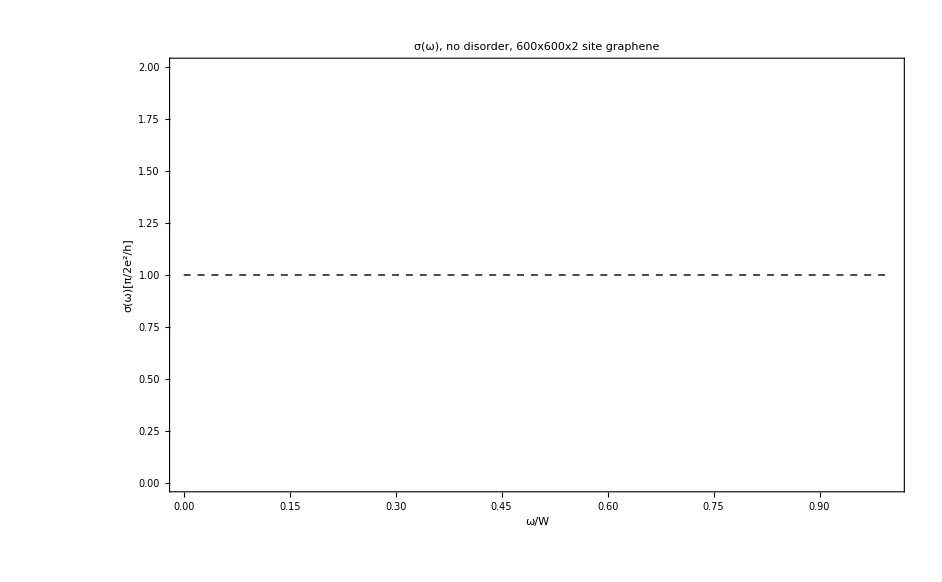

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-1,1,2./601]]; 
ListLinePlot[tempp, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

NIntegrate::inumr: The integrand -0.714286\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.4 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.4}}.

NIntegrate::inumr: The integrand -0.733464\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.36339 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.3634}}.

NIntegrate::inumr: The integrand -0.751814\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.33012 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.33012}}.

NIntegrate::inumr: The integrand -0.714286\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.4 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.4}}.

NIntegrate::inumr: The integrand -0.733464\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.36339 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.3634}}.

NIntegrate::inumr: The integrand -0.751814\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.33012 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.33012}}.

NIntegrate::inumr: The integrand -0.714286\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.4 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.4}}.

NIntegrate::inumr: The integrand -0.733464\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.36339 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.3634}}.

NIntegrate::inumr: The integrand -0.751814\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.33012 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.33012}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.791414\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.26356 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.26356}}.

NIntegrate::inumr: The integrand -0.771106\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.29684 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.29684}}.

NIntegrate::inumr: The integrand -0.791414\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.26356 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.26356}}.

NIntegrate::inumr: The integrand -0.771106\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.29684 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.29684}}.

NIntegrate::inumr: The integrand -0.791414\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.26356 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.26356}}.

NIntegrate::inumr: The integrand -0.812821\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.23028 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.23029}}.

NIntegrate::inumr: The integrand -0.771106\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.29684 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.29684}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.812821\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.23028 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.23029}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.812821\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.23028 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.23029}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.835418\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.197 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.19701}}.

NIntegrate::inumr: The integrand -0.859308\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.16373 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.16373}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.859308\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.16373 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.16373}}.

NIntegrate::inumr: The integrand -0.884604\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.13045 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.13045}}.

NIntegrate::inumr: The integrand -0.859308\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.16373 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.16373}}.

NIntegrate::inumr: The integrand -0.884604\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.13045 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.13045}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.884604\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.13045 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.13045}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.911435\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.09717 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.09717}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.939944\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.06389 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.0639}}.

NIntegrate::inumr: The integrand -0.970294\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.03062 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.03062}}.

NIntegrate::inumr: The integrand -0.939944\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.06389 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.0639}}.

NIntegrate::inumr: The integrand -0.970294\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.03062 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.03062}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.970294\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.03062 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.03062}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.714286\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.4 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.4}}.

NIntegrate::inumr: The integrand -0.715988\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.39667 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.39668}}.

NIntegrate::inumr: The integrand -0.717698\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.39334 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.39335}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.714286\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.4 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.4}}.

NIntegrate::inumr: The integrand -0.715988\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.39667 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.39668}}.

NIntegrate::inumr: The integrand -0.717698\ (-1/1 + ⅇ^1.×10^6\ Plus[« 2 »] + 1/1 + ⅇ^1.×10^6\ (0.  + ϵ))\ KuboσF[$Failed][ϵ, -1.39334 + ϵ]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.×10^-6, 1.39335}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

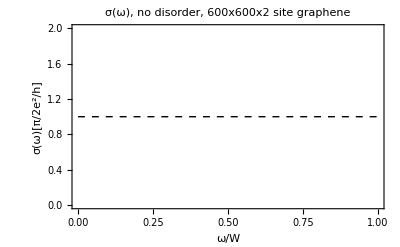

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-1.4,-1,2./601]]; 
ListLinePlot[tempp, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```